```mathematica
n=100;
```

```mathematica
H[a_,k_]:=DiagonalMatrix[Table[ 2Cos[k+a*r],{r,-n,n}]] + DiagonalMatrix[ConstantArray[1,2n],-1] + DiagonalMatrix[ConstantArray[1,2n],1];
```

```mathematica
Hof=
Flatten[
Table[
Replace[
Eigenvalues [H[a,k]],
x_->{a,x},1],
{a,0,1,0.01},{k,-Pi,Pi,0.01}],1];
```

```mathematica
o
```

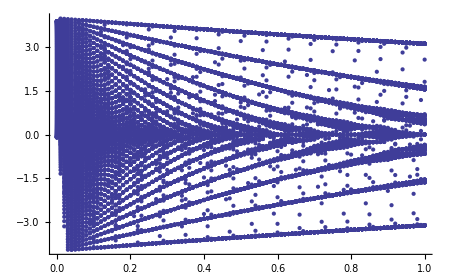

```mathematica
ListPlot[Hof]
```